### ColorMaps

This package defines color maps that associate color values with complex numbers.     These color maps are used to visualize complex-valued functions.

QComplexToColor[z,opts] |  associates a color to a complex number z. The color map is given by the option QComplexToColorMap. QComplexToColor[z] returns the result in the form Hue[h,s,b] (in the HSB system). Package: VQM`ColorMaps`.
QRGBValues[hue,lightness] |  converts color coordinates from the HLS system to color coordinates in the RGB system. It associates the RGB color values {r,g,b} to the given values of hue and lightness, assuming that the saturation is equal to 1 (maximal saturation at the given lightness). Package: VQM`ColorMaps`.
QComplexToRGBColor[z] |  returns the color RGBColor[r,g,b] of the complex number z according to the standard color map. Package: VQM`ColorMaps`.
$QComplexToColorMap[r,phi,{parameters}] |  associates a color to a complex number. Default for QComplexToColor. The complex number is given in polar form, r=Abs[z], phi=Arg[z]. The result is returned as $QComplexToColorMap[r,phi,{}] = Hue[h,s,b], in the HSB color system. The Hue h of the color is given by phi/2/Pi, the lightness is determined from r. The color map can be described as a stereographic projection from the complex plane onto the surface of the color manifold in the Hue-Lightness-Saturation system. The optional parameters are {R,bmin,bmax,lmin,lmax} specifying the radius R of the sphere, the value bmin and bmax are those values of r which belong to the minimal and maximal lightness lmin and lmax. Package: VQM`ColorMaps`.
QSaturationFromLightness[x] |  is an auxiliary function provided by the package ColorMaps. ComputesComputes the value of the saturation in the HSB-system from the lighness x (0 <= x <= 1) of the color in the HLS-system, assuming maximal HLS-saturation. Compiled for faster execution. Package: VQM`ColorMaps`.
QBrightnessFromLightness[x] |  is an auxiliary function provided by the package ColorMaps. Computes the value of the brightness in the HSB-system from the lighness x (0 <= x <= 1) of the color in the HLS-system, assuming maximal HLS-saturation. Compiled for faster execution. Package: VQM`ColorMaps`.
QHueFromArgument[arg] |  is a compiled auxiliary function provided by the package ColorMaps. Computes the Hue from the argument arg of a complex number. Package: VQM`ColorMaps`.
QLightnessFromModulus[parameters] |  defines a compiled auxiliary function that depends on certain parameters.  The parameters are given as a list of the form {R,bmin,bmax,lmin,lmax}. See the description of $QComplexToColorMap for an explanation. [r] computes the Lightness from the modulus r of a complex number. QLightnessFromModulus is provided by the package ColorMaps. Package: VQM`ColorMaps`.
QProcessColorMapOptions[opts] |  is an auxiliary function provided by the package ColorMaps. Converts a list of options into a valid list of parameters for the following color map functions: QLightnessFromModulus, $QComplexToColorMap. Package: VQM`ColorMaps`.
QVectorToColor[{u,v,w}] |  maps a three-dimensional real vector to a unique color. The color is given as a list of three real numbers (the RGB values of the color). The saturation depends on the length of the vector and the hue is defined by the direction. (red = positive x-direction, etc., the standard color circle in the xy-plane. White = positive z-direction, black = negative z-direction, 50% gray = zero vector). Package: VQM`ColorMaps`.
QSpinorToColor[{u,v}] |  maps a spinor (i.e., a C^2-vector) to a unique color. The color is given as a list of three real numbers (the RGB values of the color). This is done by first converting the spinor to a vector (using QSpinorToVector from the package VQM`Spinors`) and then applying QVectorToColor. Package: VQM`ColorMaps`.

This loads the package

```mathematica
Needs["VQM`ColorMaps`"]
```

This is an example

```mathematica
QComplexToColor[3.+2. ⅈ]
```

Hue[0.0935835,0.344475,1]

```mathematica
QComplexToRGBColor[3.+2. ⅈ]
```

RGBColor[1,0.848948,0.655525]

```mathematica
Needs["VQM`ComplexPlot`"]
```

```mathematica
QColorArrayPlot[Table[QComplexToColor[x+ⅈ y],{y,-3,3,0.5},{x,-3,3,0.5}]]
```

-Graphics-

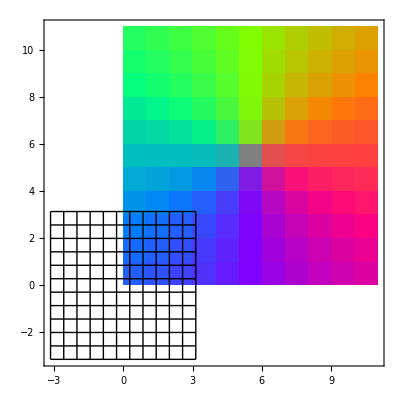

```mathematica
QColorArrayPlot[Table[RGBColor@@QVectorToColor[{x,y,0}],{y,-π,π,π/5},{x,-π,π,π/5}],MeshRange->{{-π,π},{-π,π}}]
```

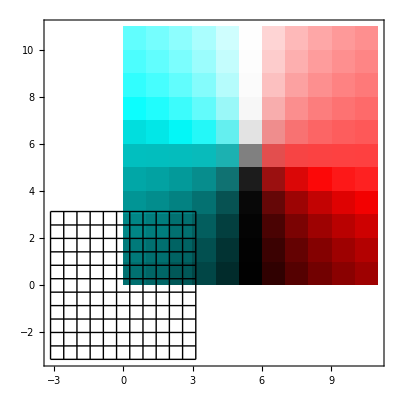

```mathematica
QColorArrayPlot[Table[RGBColor@@QVectorToColor[{x,0,z}],{z,-π,π,π/5},{x,-π,π,π/5}],MeshRange->{{-π,π},{-π,π}}]
```